## synchronize the Lorenz equations to send secret messages Problem 11.18

```mathematica
Clear["Global`*"];
```

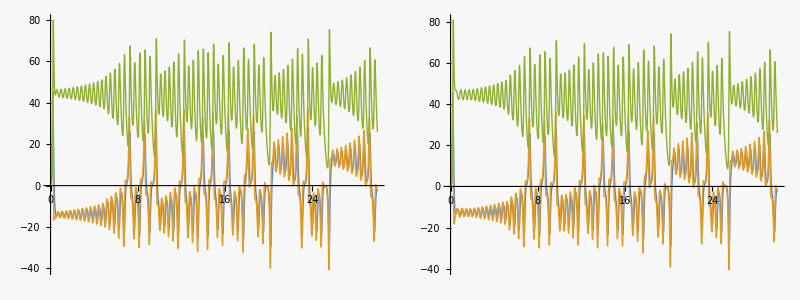

```mathematica
tend=30;σ=16; b=4;r=45.6;a=0.4;
m=  ((SquareWave[t/10]+1)/2);(* "secret message" *)  
 Subscript[eq, 1]={x'[t]==σ(y[t]-x[t]), y'[t]==x[t](r-z[t])-y[t],z'[t]==x[t]y[t]-(b+a m) z[t]};
Subscript[eq, 2]={xr'[t]==σ(yr[t]-xr[t]), yr'[t]==x[t](r-zr[t])-yr[t],zr'[t]==x[t]yr[t]-b zr[t]};
Subscript[init, 1]={x[0]==1,y[0]==1,z[0]==1};
Subscript[init, 2]={xr[0]==0,yr[0]==0,zr[0]==0};

{xs,ys,zs,xrs,yrs,zrs}=NDSolveValue[{Subscript[eq, 1], Subscript[eq, 2],Subscript[init, 1],Subscript[init, 2]},{x,y,z,xr,yr,zr},{t,0,tend}];

Subscript[p, 1]=Plot[{xs[t],ys[t],zs[t]},{t,0,tend},ImageSize->300];
Subscript[p, 2]=Plot[{xrs[t],yrs[t],zrs[t]},{t,0,tend},PlotRange->All,ImageSize->300];
Grid[{{Subscript[p, 1],Subscript[p, 2]}},Spacings->2]
```

```mathematica
ParametricPlot3D[{xs[t],ys[t],zs[t]},{t,0,tend},ImageSize->300]
```

-Graphics3D-

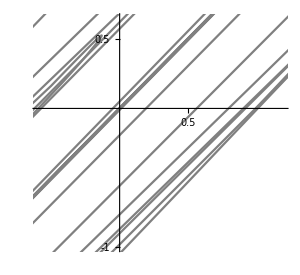

```mathematica
ParametricPlot[{xs[t],xrs[t]},{t,0,tend},ImageSize->300]
```

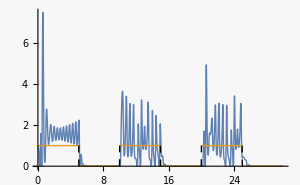

```mathematica
e1=(xs[t]-xrs[t])^2;
Plot[{e1,m},{t,0,tend},ImageSize->300,PlotRange->All]
```

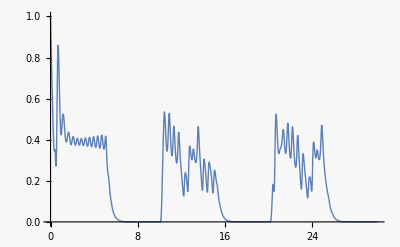

```mathematica
ws=NDSolveValue[{w'[t]+4w[t]==e1,w[0]==1},w,{t,0,tend}];
Plot[ws[t],{t,0,tend}]
```

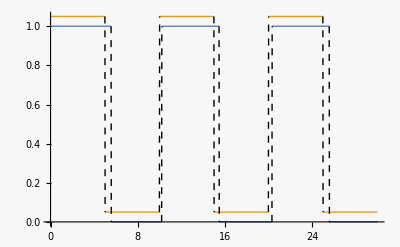

```mathematica
Plot[{(Sign[ws[t]-0.1]+1)/2,m+0.05},{t,0,tend}]
```

Export data

```mathematica
dt=0.01;
xst=Table[xs[t],{t,0,tend,dt}];
yst=Table[ys[t],{t,0,tend,dt}];
zst=Table[zs[t],{t,0,tend,dt}];
xrst=Table[xrs[t],{t,0,tend,dt}];
wst=Table[ws[t],{t,0,tend,dt}];
(* 
SetDirectory[NotebookDirectory[]];Export["lorenz.dat",Flatten/@Transpose[{xst,yst,zst,xrst,wst}],"Table"];
*)
```